```mathematica
ClearAll["Global'*"];
(* PlotLegends is now obsolete*) 
memoryTem=0;
mtxw=320; mtxh=240; sw=4; sh=3; 
redw=Round[mtxw/sw]; redh=Round[mtxh/sh];
Temperaturethreshold=.3;  showmesh=False;TechError=0.05;
FilterForErrorMagnitude1=1;
colorsGoody={RGBColor[0.05374,0,0.333],RGBColor[0.0979,0,0.467],RGBColor[0,0,1],RGBColor[0.2,1,0.96],RGBColor[0,0.93,0.07519],RGBColor[1,1,0],RGBColor[1,0,0],Darker[RGBColor[1,0,0],.4]};
f[x_]:=N[Sqrt@Sqrt[Sin[Pi*(x/mtxw)]]];
(*Plot[f[y],{y,1,ThermW}]*)
data1=Array[{#1-0.5,#2-0.5,f[#1]}&,{mtxw,mtxh}];

For[i=1,i≤mtxw,i++,{
For[j=1,j≤mtxh,j++,{

If[i≥IntegerPart[mtxw*0.4]&&i≤IntegerPart[mtxw*0.6]&&j≥IntegerPart[mtxh*0.3]&&j≤IntegerPart[mtxh*0.7],data1[[i,j,3]]=0.8];
If[i≥IntegerPart[mtxw*0.6]&&i≤IntegerPart[mtxw*0.7]&&j≥IntegerPart[mtxh*0.45]&&j≤IntegerPart[mtxh*0.55],data1[[i,j,3]]=data1[[i,j,3]]+2*TechError*RandomReal[]*(-1)^RandomInteger[1]];

data1[[i,j,3]]=data1[[i,j,3]]+2*TechError*RandomReal[]*(-1)^RandomInteger[1];

}]
}]

(*Begin Rotation script for real thermogram RESHAPED ARRAY*)
(*For[i=1,i≤mtxw,i++,{
For[j=1,j≤Round[mtxh/2],j++,{
memoryTem=data1[[(i-1)*mtxh+j,3]];
data1[[(i-1)*mtxh+j,3]]=data1[[(i-1)*mtxh+(mtxh+1-j),3]];(*5*RandomReal[]*(-1)^RandomInteger[1]*);
data1[[(i-1)*mtxh+(mtxh+1-j),3]]=memoryTem(*5*RandomReal[]*(-1)^RandomInteger[1]*);
}]
}]
Print["CheckPoint#1  - the matrix rotation was done - {1..320,1..240}->{1..320,240..1}}"]  *)
 (*End Rotation script for real thermogram*)


data1=ArrayReshape[data1,{mtxh*mtxw,3}];

(*Print the plot of input thermogram*)
ListDensityPlot[data1,PlotRange->All,ColorFunction->GrayLevel,Mesh->showmesh,Mesh->{redw-1,redh-1},ClippingStyle->Automatic,AspectRatio->mtxh/mtxw,PlotLegends->Placed[Automatic,Below],ColorFunctionScaling->True,InterpolationOrder->0]
```

```mathematica
(*TE*)
```

```mathematica
-Graphics-
-Graphics-
```

```mathematica
-Graphics-
-Graphics-
```

```mathematica
(*2TE*)
-Graphics-
-Graphics-
-Graphics-
```

```mathematica
RecNoiseAnim=Manipulate[Binarize[Import["C:\\A\\Notes\\PRG\\W\\WolfThermography\\RecnRecNoise.tiff"],a],{a,0,1,0.01}]
(*Export["C:\\A\\Notes\\PRG\\W\\WolfThermography\\RecNoiseBinarizeAnim.swf",RecNoiseAnim]*)
```

```mathematica
img1=-Graphics-; img2=-Graphics-;
ImageSubtract[img1,img2]
```

-Graphics-

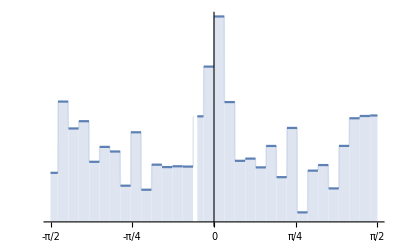

```mathematica
img=-Graphics-;
o=Flatten@ImageData@GradientOrientationFilter[img,3];
w=Flatten@ImageData@GradientFilter[img,3];
𝒜=WeightedData[o,w];
𝒟=HistogramDistribution[𝒜];
Plot[PDF[𝒟,x],{x,-π/2,π/2},Filling->Axis,PlotRange->All,Ticks->{Range[-π/2,π/2,π/4]}]
```